# NUSWorkshop Hackathon code submission - Rahul Jaiswal (rahul@nus.edu.sg)

This notebook has three segments:
	(1) Prediction Models using Mathematica predict functions
	(2) Linear regression model written in Python (Running via “External Evaluate Function” ) - Assuming you have required python packages installed in a python distribution (That is added to system’s path)
	(3) Web-service using Mathematica’s Prediction Module ( Random Forest method )

## 1. Native python code (Sklearn Linear Regression)Using “ExternalEvaluate” function

Linear Regression using sklearn library

from sklearn import linear_model
from sklearn import svm
from sklearn import model_selection

classifiers = [
    svm.SVR(),
    linear_model.SGDRegressor(),
    linear_model.BayesianRidge(),
    linear_model.LassoLars(),
    linear_model.ARDRegression(),
    linear_model.PassiveAggressiveRegressor(),
    linear_model.TheilSenRegressor(),
    linear_model.LinearRegression()]

from pandas import read_excel
df=read_excel('obs_data_w.xlsx',sheet_name='Sheet1')

Y=df.iloc[:,0].values

X=df.iloc[:,[1,3]].values

test_size = 0.33
seed = 7
X_train, X_test, Y_train, Y_test = model_selection.train_test_split(X, Y, test_size=test_size, random_state=seed)

trainingData    = X_train
trainingScores  = Y_train
predictionData  = X_test

#trainingData    = np.array([ [2.3, 4.3, 2.5],  [1.3, 5.2, 5.2],  [3.3, 2.9, 0.8],  [3.1, 4.3, 4.0]  ])
#trainingScores  = np.array( [3.4, 7.5, 4.5, 1.6] )
#predictionData  = np.array([ [2.5, 2.4, 2.7],  [2.7, 3.2, 1.2] ])

for item in classifiers:
    print(item)
    clf = item
    clf.fit(trainingData, trainingScores)
    print(clf.predict(predictionData),'\n')

# 2. Prediction Models Using Wolfram Predict Function Running as a web-service at http://192.168.1.1 (NUS Networks Only)

## Importing Data

Data Import from Excel Sheet

```mathematica
datafile=FileNameJoin[{NotebookDirectory[],"obs_data_w.xlsx"}];
```

```mathematica
SemanticImport[datafile]
```

Dataset[<>]

Curating data

```mathematica
datasetnb = Import[datafile][[1]];
```

```mathematica
datasetnb =Drop[ datasetnb,1];
```

```mathematica
datalengthnb = Length[datasetnb];
```

## Assigning data to Attributes

```mathematica
Voltage = {};
CurrentDensity= {};
Temparature = {};
Uncertanity= {};
```

```mathematica
c1 = 0;
While[(c1 += 1) <datalengthnb ,
  {
    
    Voltage = Append[Voltage, datasetnb[[c1]][[2]]];
    Temparature = Append[Temparature, datasetnb[[c1]][[3]]];
    Uncertanity = Append[Uncertanity, datasetnb[[c1]][[4]]];
    CurrentDensity = Append[CurrentDensity, datasetnb[[c1]][[5]]];
    };
  ];
```

## Creating data-sets (training and test) for the model

Input set

```mathematica
inputset= Transpose[{Temparature,CurrentDensity}];
```

Complete set

```mathematica
completeset= {};
For[i=1,i<datalengthnb,i++,completeset = Append[completeset,inputset[[i]] -> Voltage[[i]]]];
```

Randomizing Complete set

```mathematica
CompletesetRandomized=completeset[[PermutationList@RandomPermutation@Length[completeset]]];
```

```mathematica
If[Length[completeset]==Length[CompletesetRandomized],FlagforMemoryleak=0,FlagforMemoryleak=1];
```

Creating training and test data-sets

```mathematica
TrainTestRatio = 0.8;
{TrainingSet,TestSet}=TakeDrop[CompletesetRandomized,Round[Length[CompletesetRandomized]*TrainTestRatio]];
```

## Running ‘Predict’ function using different prediction Methods

Linear Regression prediction Method

```mathematica
LinearPrediction= Predict[TrainingSet,Method->"LinearRegression"];
infolinearreg = Quiet[PredictorInformation[LinearPrediction]];
```

Neural Network prediction Method

```mathematica
NeuralNetwordPrediction = Quiet[Predict[TrainingSet,Method->"NeuralNetwork"]];		
infoNeuralNetwork = Quiet[PredictorInformation[NeuralNetwordPrediction]];
```

Nearest Neighbors prediction Method

```mathematica
NearestNeighborPrediction= Predict[TrainingSet,Method->"NearestNeighbors"];	
infoNN = Quiet[PredictorInformation[NearestNeighborPrediction]];
```

Random Forest prediction Method

```mathematica
RandomForestPrediction= Predict[TrainingSet,Method->"RandomForest"];
infoRF = Quiet[PredictorInformation[RandomForestPrediction]];
```

## Difference between actual and predicted values (Using Test Data)

Linear Regression prediction Method

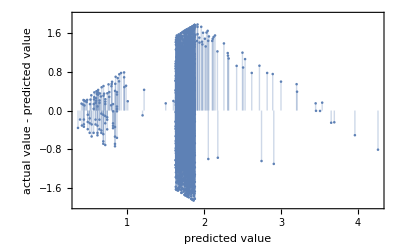

0.99725

```mathematica
PredictorMeasurements[LinearPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[LinearPrediction,TestSet,"StandardDeviation"]
```

Neural Network prediction Method

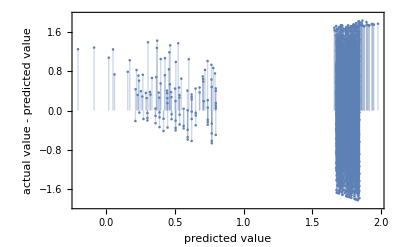

1.02603

```mathematica
PredictorMeasurements[NeuralNetwordPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[NeuralNetwordPrediction,TestSet,"StandardDeviation"]
```

Nearest Neighbors prediction Method

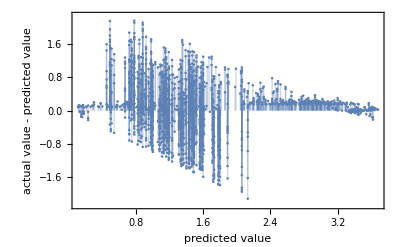

0.705497

```mathematica
PredictorMeasurements[NearestNeighborPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[NearestNeighborPrediction,TestSet,"StandardDeviation"]
```

Random Forest prediction Method

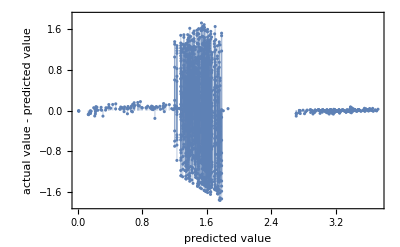

0.784157

```mathematica
PredictorMeasurements[RandomForestPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[RandomForestPrediction,TestSet,"StandardDeviation"]
```

## Predicting step voltage for 400 K

```mathematica
DesiredConditions = {400,0.1};
```

Linear Regression prediction Method

```mathematica
PredictedVonbyLRMethod = LinearPrediction[DesiredConditions]
```

1.25183

Neural Network prediction Method

```mathematica
PredictedVonbyNeurNetMethod = NeuralNetwordPrediction[DesiredConditions]
```

1.00982

Nearest Neighbors prediction Method

```mathematica
PredictedVonbyNearNeigMethod = NearestNeighborPrediction[DesiredConditions]
```

1.71

Random Forest prediction Method

```mathematica
PredictedVonbyRFMethod = RandomForestPrediction[DesiredConditions]
```

1.6994